```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
kB = 1.38 10^-23;
ℏ = 1.055 10^-34;
m = 2.838464 10^-25;
μB = 9.27400968 10^-24;
dzB = 23.5;
```

## Functions

```mathematica
η[ν_]:= (μB dzB)/(ℏ ν)√(ℏ/(2 m ν));
```

```mathematica
P1[Ω_,Δ_,t_,τ_] := Ω^2/(Ω^2+Δ^2)(((Sin[1/2 √(Ω^2+Δ^2)t])^2-0.5)Exp[-t/τ]+0.5)
Ωsb[Ω_, η_] := Ω η
P[n_,nbar_] := 1/(1+nbar)(nbar/(1+nbar))^n;
PRSB[Ω_,Δ_,t_,τ_,nbar_, nlevels_] := Sum[P[n,nbar] P1[√n Ω,Δ,t,τ],{n,0,nlevels}]
PBSB[Ω_,Δ_,t_,τ_,nbar_, nlevels_] := Sum[P[n,nbar] P1[√(n+1)Ω,Δ,t,τ],{n,0,nlevels}]
```

## Parameters

```mathematica
ν = 2π 266 10^3; (*Secular Frequency *)
τ = 2 10^-3; (* Decoherence decay constant *)
Ω = 2π 47.38 10^3; (* Carrier Rabi Frequency *)
nbar = 80; (* Average motional state *)
nlevels = 200;
η[ν]
```

0.0130335

```mathematica
PRSB[Ωsb[Ω, η[ν]],2 π 500,100 10^-6,τ,50, nlevels]
P1[Ω, 2 π 500, 100 10^-6, τ]
```

0.615518

0.534981

```mathematica
n = 200;
 P1[√(n+1)Ωsb[Ω, η[ν]],2 π 500,100 10^-6,τ]//N
P[n, 50]//N
PBSB[Ωsb[Ω, η[ν]], 2 π 500, 100 10^-6, τ, 50, n]
```

0.159136

0.00037359

0.627888

## Input

```mathematica
(* Input list of probabilites *)
```

```mathematica
pup = {1.5494014760459318,2.6760423435425413,4.929548519234583,18.450649592297655,22.957861747811968,25.211270890310356,35.35214658722074,53.3802882555793,62.39447163318032,62.39447163318032,68.02815454931044,57.88735947229999,49.99999999999999,60.140765556595234,47.7464767051668,49.99999999999999,42.1126405277,63.52101148484566,47.7464767051668,51.126760857165976,56.76059373435906,42.1126405277,46.6197117444207,52.253523294833826,45.49294421646051,55.63382492082491,45.49294421646051,37.605528366819975,46.6197117444207,44.36617507917514,44.36617507917514};
Tstep = 10; (* Time step of experiment *)
```

## Logic

```mathematica
pup = pup/100 (* Normalise probabilities over 1 *)
xList = Table[Tstep * i, {i, 0, Length[pup] - 1}];
```

{0.015494,0.0267604,0.0492955,0.184506,0.229579,0.252113,0.353521,0.533803,0.623945,0.623945,0.680282,0.578874,0.5,0.601408,0.477465,0.5,0.421126,0.63521,0.477465,0.511268,0.567606,0.421126,0.466197,0.522535,0.454929,0.556338,0.454929,0.376055,0.466197,0.443662,0.443662}

```mathematica
{0.01549401476045932,0.026760423435425413,0.049295485192345834,0.18450649592297655,0.2295786174781197,0.25211270890310356,0.3535214658722074,0.533802882555793,0.6239447163318033,0.6239447163318033,0.6802815454931045,0.5788735947229999,0.49999999999999994,0.6014076555659523,0.477464767051668,0.49999999999999994,0.421126405277,0.6352101148484566,0.477464767051668,0.5112676085716598,0.5676059373435907,0.421126405277,0.466197117444207,0.5225352329483383,0.45492944216460507,0.556338249208249,0.45492944216460507,0.37605528366819974,0.466197117444207,0.44366175079175146,0.44366175079175146}
```

{0.015494,0.0267604,0.0492955,0.184506,0.229579,0.252113,0.353521,0.533803,0.623945,0.623945,0.680282,0.578874,0.5,0.601408,0.477465,0.5,0.421126,0.63521,0.477465,0.511268,0.567606,0.421126,0.466197,0.522535,0.454929,0.556338,0.454929,0.376055,0.466197,0.443662,0.443662}

## Output

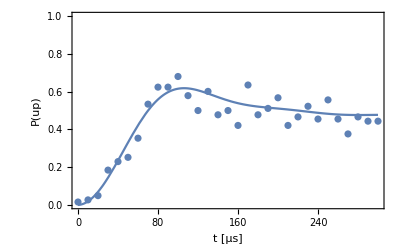

```mathematica
Show[Plot[{PRSB[Ωsb[Ω, η[ν]],2 π 500,t 10^-6,τ,50, nlevels]},{t,0,Max[xList]},  PlotRange->{{0, Max[xList]},{0, 1}}],ListPlot[Transpose[{xList, pup}]], Frame-> True, FrameLabel-> {"t [μs]", "P(up)"}, FrameStyle-> { Thick}]
```

```mathematica
nlmfit = NonlinearModelFit[pup, PBSB[Ωsb[Ω, η[ν]],δ,t 10^-6,τ,nb, nlevels], {{nb, 50}, {δ, 2π 200}}, t, MaxIterations->10000]
```

General::munfl: 1.49699×10^-299 3.79342×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.93528×10^-301 3.77188×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.75544×10^-303 3.75059×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: 2.03196×10^-300 3.7957×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.93903×10^-302 3.77413×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.63595×10^-304 3.75281×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FittedModel[0.+«179»+0.00058302 (0.5+ⅇ^(-t/2000) (-0.5+Sin[0.026028 t]^2))]

```mathematica
nlmfit["BestFitParameters"]//Normal
```

General::munfl: 2.03196×10^-300 3.7957×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.93903×10^-302 3.77413×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.63595×10^-304 3.75281×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{nb→50.5853,δ→-0.38061}

General::munfl: 2.03196×10^-300 3.7957×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.93903×10^-302 3.77413×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.63595×10^-304 3.75281×10^-10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{nb→50.5853,δ→-0.38061}

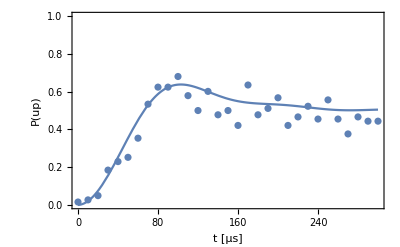

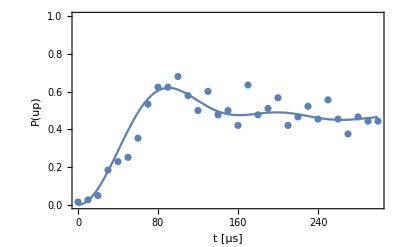

```mathematica
nlmfit["BestFitParameters"]//Normal
Show[Plot[{PBSB[Ωsb[Ω, η[ν]],0,t 10^-6,τ,55, nlevels]},{t,0,Max[xList]},  PlotRange->{{0, Max[xList]},{0, 1}}],ListPlot[Transpose[{xList, pup}]], Frame-> True, FrameLabel-> {"t [μs]", "P(up)"}, FrameStyle-> { Thick}]

Show[Plot[{PBSB[Ωsb[Ω, η[ν]],2500,t 10^-6,τ,nbar, nlevels]},{t,0,Max[xList]},  PlotRange->{{0, Max[xList]},{0, 1}}],ListPlot[Transpose[{xList, pup}]], Frame-> True, FrameLabel-> {"t [μs]", "P(up)"}, FrameStyle-> { Thick}]
```